0

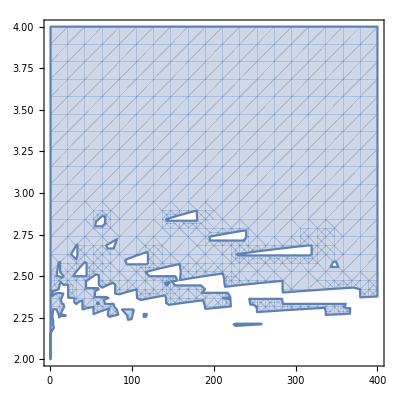

```mathematica
Remove[f,v,a];
l23=Log2[3];
f[v_,a_]:=IntegerPart[l23*IntegerPart[(Log2[(3*v-v*2^a+1)/(4-2^a)])/(a-l23)]+Log2[v]]+1-a*IntegerPart[(Log2[(3*v-v*2^a+1)/(4-2^a)])/(a-l23)];
Print[f[310,3]];
RegionPlot[0≤f[v,a],{v,1,400},{a,2,4}]
(*Plot3D[f[v,a],{v,1,200},{a,1,10}]*)
```